# Jacobians, Eigenvalues, and Areas Oh My!

# My!

The ODE problem function is too messy. Lets look at a simple function f:ℝ^2→ℝ^2 and a point xStar.

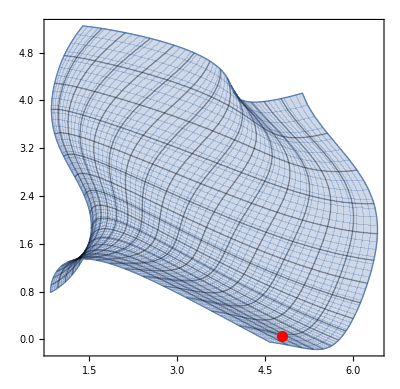

```mathematica
f[{x1_,x2_}]:= {
x1 +Sin[x1 x2 +Cos[x1^2+ Sin[x2]]]+ x2^2,
x2 Cos[x1+x2]+x1^2+ArcTan[x1+ x2 x1 + 1]}
xStar={0.3,1.9};
BigPic=ParametricPlot[f[{x1,x2}], {x1, 0,2},{x2,0,2},
Mesh->Automatic,
Epilog->{Red, PointSize[0.02],Point[f[xStar]]}]
```

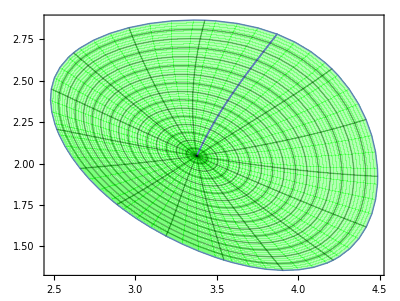

```mathematica
ϵ=0.3;
CloseUpPic=ParametricPlot[ f[xStar+r {Cos[θ],Sin[θ]}],
{r, 0, ϵ},{θ,0, 2π},
Mesh->Automatic,
PlotStyle->Green]
```

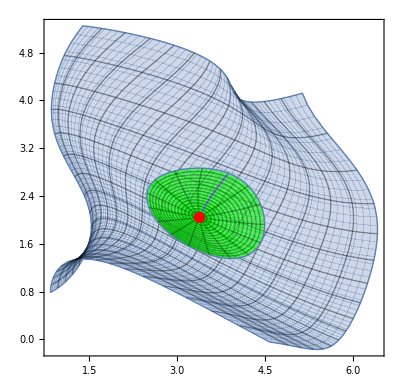

```mathematica
Show[ BigPic,CloseUpPic]
```

What has the Jacobian got to do with this

4.8405

0.457662

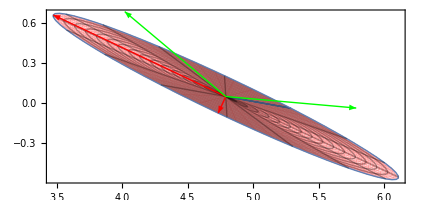

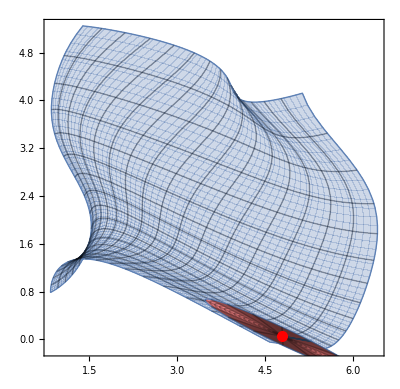

```mathematica
J[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}];
A=J[xStar];
{U,W,V}= SingularValueDecomposition[A];
σ1=W⟦1,1⟧
σ2=W⟦2,2⟧
{u1,u2}=Uᵀ;
{{λ1,λ2},{v1,v2}}=Eigensystem[A];
LinearCloseUpPic=ParametricPlot[ f[xStar]+r A.{Cos[θ],Sin[θ]},
{r, 0, ϵ},{θ,0, 2π},
Mesh->Automatic,
PlotStyle->Pink,
Epilog->{
{Red,Arrow[{f[xStar], f[xStar]+ϵ σ1 u1}],Arrow[{f[xStar], f[xStar]+ϵ σ2 u2}]},
{Green,Arrow[{f[xStar], f[xStar]+v1}],Arrow[{f[xStar], f[xStar]+v2}]}}
]
Show[BigPic, LinearCloseUpPic]
```

### Summary

The SVD of a real matrix A is A=U.Σ.Vᵀ where Uᵀ.U=I, Vᵀ.V=I and Σ is a diagonal matrix with ordered non-negative entries σ_1≥σ_2≥…≥0.

#### ℝ^2

For a smooth function f:ℝ^2->ℝ^2 a small disk around any point x_* is mapped into an ellipse around f(x_*).  The major axis of the ellipse is in the direction u_1 and is of length σ_1. The minor axis of the ellipse is in the directions u_2 and is of length σ_2.   The ellipse has area σ_1 σ_2 times the area of the small disk.

#### ℝ^3

For a smooth function f:ℝ^3->ℝ^3 a small sphere around any point x_* is mapped into an ellipsoid around f(x_*).  The axis of the ellipsoid are σ_1 u_1, σ_2 u_2, and σ_3 u_3. The volume of the ellipsoid is σ_1 σ_2 σ_3 times the volume of the small sphere.

```mathematica
f[{x1_,x2_,x3_}]:= {
Sin[x1 + Cos[x2^2+Sin[x1 x3]]^3]+x2, 
Cos[x2 + Cos[x1^3+ArcTan[x1 x3]]^3]+x1,
x2+x1 x3 - Sin[x1*x2]}
J[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}];
xStar={1.0,0.3,2.5};
ϵ=0.02;
TabView[{
"Input"->ParametricPlot3D[ xStar+ϵ {Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ], Cos[ϕ]},
{θ,0, 2π},{ϕ,0, π},
PlotLabel->StringForm["ϵ=``",ϵ]],
"Output"-> ParametricPlot3D[ f[xStar+ϵ {Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ], Cos[ϕ]}],
{θ,0, 2π},{ϕ,0, π},
PlotLabel->StringForm["ϵ=``",ϵ]] ,
"Output+"-> (JStar=J[xStar];
{UStar,SStar,VStar}=SingularValueDecomposition[JStar];
fStar=f[xStar];
Show[
ParametricPlot3D[ f[xStar+ϵ {Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ], Cos[ϕ]}],
{θ,0, 2π},{ϕ,0, π},
PlotStyle->Opacity[0.5],
PlotLabel->StringForm["ϵ=``",ϵ]],
Graphics3D[{Red,
Arrow[{fStar,fStar+ϵ SStar⟦1,1⟧UStar⟦All,1⟧}],
Arrow[{fStar,fStar+ϵ SStar⟦2,2⟧UStar⟦All,2⟧}],
Arrow[{fStar,fStar+ϵ SStar⟦3,3⟧UStar⟦All,3⟧}]}]]
 )}]
```

123

# Estimating a Jacobian!

The above is all fine and dandy but we do not (and can not) have a formula for the solution in our ODEs.  There are two things we can do.

We can solve the ODEs for nearby points.  This is essentially a finite difference approximation.

We can differentiate the ODE with respect to the input

The first is conceptually easier.

### Finite Difference Approximation to the Gradient of the Rosseler First Return Map

```mathematica
{a,b,c}={0.2,0.2,5.7};
f[{x_,y_,z_}]:= {-y-z,x + a*y, b +z*(x-c)}
ForwardMap[p0_List]:=Module[{p,t,end},
Catch[
NDSolveValue[{p'[t]==f[p[t]],p[0]==p0},p,{t,0, 10^3},
Method->{"EventLocator",
"Event":>((p[t]-{0.007026204834100129,-0.035131024170500645,0.035131024170500645}). {1,-1,0}),
"EventAction":>Throw[end=p[t],"StopIntegration"],
"Direction"->-1}]; end]
]
```

I need to pick a point on my plane and two nearby points that make a right angle at  the chosen point.

```mathematica
h= 0.0001;
p0={2.0,2.0,5.0};
v1=Normalize[{1.0,1.0,0.0}];
v2=Normalize[{0.0,0.0,1.0}];
p1=p0+h v1;
p2=p0+h v2;
p3=p0+h(v1+v2);
{P0,P1,P2,P3}= Map[ForwardMap,{p0,p1,p2,p3}];
{D1,D2,D3}={P1-P0,P2-P0,P3-P0}/h;
D1 + D2-D3;
MatrixForm[JMat={D1,D2}⟦All,{1,3}⟧];
SingularValueDecomposition[JMat]
```

{{{-0.996827,0.0795954},{0.0795954,0.996827}},{{1.15919,0.},{0.,3.4586×10^-7}},{{-0.998212,-0.0597767},{-0.0597767,0.998212}}}

If h  is small enough then we can guess (well it is a lot better than a guess) where